# Simple Task 7

Brian Carlson 2-24-2014

## Problem 1

#### Helper Function

```mathematica
returnCoord[coord1_,coord2_,length_]:=Module[{distance=EuclideanDistance[coord1,coord2],deltaX=coord1[[1]]-coord2[[1]],deltaY=coord1[[2]]-coord2[[2]],angle,magnitude,ratio},
ratio=deltaY/deltaX;
angle =ArcTan[Abs[ratio]];
magnitude=If[distance-length>0,distance-length,0];
Return[{N[magnitude *Cos[If[Sign[deltaX]==-1,π,0]+Sign[ratio]*angle]]+coord2[[1]],N[magnitude*Sin[If[Sign[deltaX]==-1,π,0]+Sign[ratio]*angle]]+coord2[[2]]}]
]
```

#### Solution

```mathematica
Robberarrest[RobberCo_,Police1Co_,Police2Co_,speed_,timestep_,stepnumb_]:= Module[{length=speed*timestep*stepnumb},
Graphics[{Line[{{returnCoord[Police1Co,RobberCo,length],Police1Co},{returnCoord[Police2Co,RobberCo,length],Police2Co}}],PointSize[Large],Black,Point[{Police1Co,Police2Co}],Red,Point[RobberCo]}]
]
```

### Test Cases

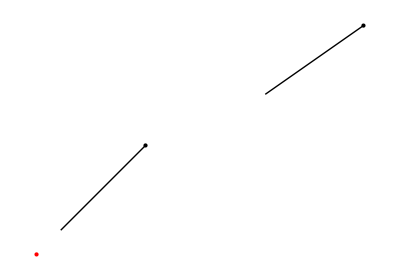

```mathematica
Robberarrest[{-1,-1},{2,1.1},{0,0},1,.01,110]
```

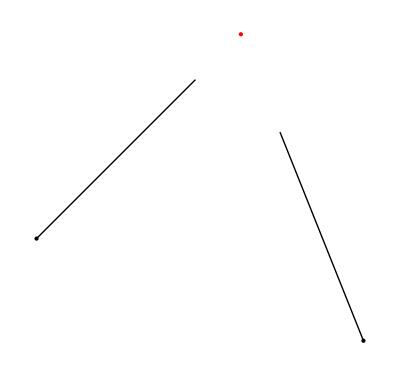

```mathematica
Robberarrest[{0,0},{-1,-1},{.6,-1.5},1,.01,110]
```

```mathematica
Manipulate[Robberarrest[{0,1},{-1,-1},{2,1.1},1,.01,k],{k,1,1000}]
```

## Extra: A Generalized Solution

It still has a few bugs, but, with the helper function it tends to work for any number of police/points/type of personnel.

```mathematica
generalRobberarrest[RobberCo_,policeCo_,speed_,timestep_,stepnumb_]:= Module[{length=speed*timestep*stepnumb,i,displayList={},pointList={},distances=EuclideanDistance[#,RobberCo]&/@policeCo, color},

For[i=1,i≤ Length[policeCo],i++,
color=Switch[i,Position[distances,Max[distances]],Red,Position[distances,Min[distances]],Green,_,Black];
AppendTo[displayList,Graphics[color,Line[{returnCoord[policeCo[[i]],RobberCo,length],policeCo[[i]]}]
]];
AppendTo[pointList,policeCo[[i]] ]
];
AppendTo[displayList,Graphics[{PointSize[Large],Black,Point[pointList],Red,Point[RobberCo]}]];
Show[displayList]
]
```

```mathematica
{#,1}&/@{1,2,3,4,5,6}
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1}}

#### Test Cases

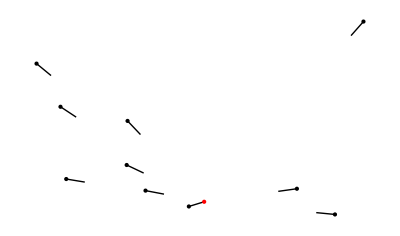

```mathematica
cops=Table[{RandomReal[{-10,10}],RandomReal[{-10,10}]},{i,1,10}];
generalRobberarrest[{0,0},cops,1,.01,100]
```

```mathematica
cops=Table[{RandomReal[{-10,10}],RandomReal[{-10,10}]},{i,1,10}];
Manipulate[generalRobberarrest[{RandomReal[{-10,10}],RandomReal[{-10,10}]},cops,1,.01,k],{k,1,1000}]
```

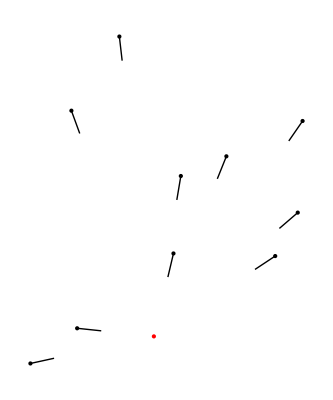

```mathematica
cops=Table[{RandomReal[{-10,10}],RandomReal[{-10,10}]},{i,1,10}];
generalRobberarrest[{RandomReal[{-10,10}],RandomReal[{-10,10}]},cops,1,.01,100]
```